FInd gnd state solution for arbitrary l

```mathematica
With[{χl0=r^(l+1)ⅇ^(-b r)},
-1/2 D[χl0, r,r]+((l(l+1))/(2 r^2)-1/r)χl0==Subscript[ϵ, l,0] χl0//Simplify]
```

ⅇ^(-b r) r^l (2-2 b (1+l)+b^2 r+2 r ϵ_(l,0))==0

```mathematica
Collect[%,r]
```

ⅇ^(-b r) (2-2 b (1+l)) r^l+ⅇ^(-b r) r^(1+l) (b^2+2 ϵ_(l,0))==0

from which b=1/(l+1), ϵ_(l 0)=-1/(2(l+1)^2)

Find P_(4s):

```mathematica
Subscript[W, l_]:=1/(l+1)-(l+1)/s
```

```mathematica
(A†)_l_@f_:=-D[f, s]+Subscript[W, l] f
```

use A† to do 4f→4d→4p→4s

```mathematica
Subscript[χ, l_,0]:=s^(l+1)ⅇ^(-s/(l+1))
```

```mathematica
P4s=(A†)_0@(A†)_1@(A†)_2@Subscript[χ, 3,0]//Simplify
```

35/64 ⅇ^(-s/4) s (-192+144 s-24 s^2+s^3)

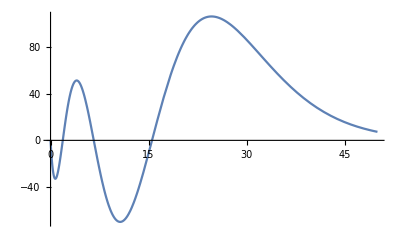

```mathematica
Plot[P4s,{s,0,50}]
```

Check that this function indeed solves SE:

```mathematica
SE[Pnl_,l_,ϵ_]:=-1/2 D[Pnl, s,s]+((l(l+1))/(2 s^2)-1/s)Pnl==ϵ Pnl
```

```mathematica
SE[P4s,0,-1/(2 4^2)]//Simplify
```

True